```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

```mathematica
cols={RGBColor[1, 0.2, 0],RGBColor[0.5, 0.8, 0],RGBColor[0.2, 0.6, 1]};
NBodySolve[PosList_,VelList_,MassList_,T_]:=Module[{Nb,nds,Tmax,prolog,funsToPlot,names,eqs}, 
Nb=Length[PosList];
names=Table[Unique["r"],{Nb}];
eqs=Flatten[Table[{names⟦i⟧[0]==PosList⟦i⟧,names⟦i⟧'[0]==VelList⟦i⟧,names⟦i⟧''[t]==Sum[If[i==j,0,MassList⟦j⟧/Norm[names⟦j⟧[t]-names⟦i⟧[t]]^3(names⟦j⟧[t]-names⟦i⟧[t])],{j,1,Nb}]},{i,1,Nb}]];
nds=NDSolve[eqs,names,{t,0,T}];

Function[t,(#[t]&/@names)/.nds⟦1⟧]
]//Quiet;
```

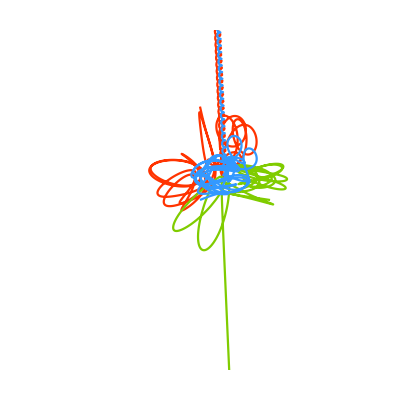

```mathematica
T=60;
sol=NBodySolve[{{0,4},{3,0},{0,0}},{{0,0},{0,0},{0,0}},{3,4,5},60]; 
ParametricPlot[sol[t]//Evaluate,{t,0,T},PlotStyle->cols,Frame->False,PlotRange->7{{-1,1},{-1,1}},AspectRatio->1,Axes->False,FrameTicks->False]
```

```mathematica
pic[t_]:=Module[{points,op,r},
lt=2;np=250;
points=(sol/@Subdivide[Max[0,t-lt],t,np])ᵀ;
op=Outer[Opacity[#2,#1]&,cols,Subdivide[0,1,np]];
r=.08;
Return@Graphics[{AbsoluteThickness[1.5],Line[#1,VertexColors->#2]&@@@({points,op}ᵀ),{cols,Disk[#⟦-1⟧,r]&/@points}ᵀ},PlotRange->{{-3,5},{-3,5}},AspectRatio->1,Background->White];
]

Manipulate[pic[tt],{tt,0,T}]
```